```mathematica
comment[c_,val_]:=Module[{}, Print[c]; val];
atNotebook[path_]:=FileNameJoin[{NotebookDirectory[],path}];
Second[xs_]:=xs[[2]];
```

```mathematica
ClearAll[m0];ClearAll[Γ0];ClearAll[S];ClearAll[L0];ClearAll[decays];

(** Nucleons **)
m0[p938]=0.938;Γ0[p938]=0.;S[p938]=1/2;L0[p938]=0;

m0[p1535]=1.530;Γ0[p1535]=0.150;S[p1535]=1/2;L0[p1535]=0;
decays[p1535]={
{{p938,pi},0.42},
{{p938,eta},0.45},
{{p938,sigma},0.06},
{{p1440,pi},0.07}
};

m0[p1650]=1.650;Γ0[p1650]=0.125;S[p1650]=1/2;L0[p1650]=1;
decays[p1650]={
{{p938,pi},0.56},
{{p938,eta},0.15},
{{Lambda,Ka},0.05},
{{Δ1232,pi},0.08},
{{p938,sigma},0.06},
{{p1440,pi},0.10}
};

m0[p1520]=1.515;Γ0[p1520]=0.115;S[p1520]=3/2;L0[p1520]=1;
decays[p1520]={
{{p938,pi},0.60},
{{Δ1232,pi},0.20},
{{p938,rho},0.20}
};

m0[p1700]=1.720;Γ0[p1700]=0.200;S[p1700]=3/2;L0[p1700]=1;
decays[p1700]={
{{p938,pi},0.13},
{{p938,omega},0.22},
{{Δ1232,pi},0.60},
{{p1440,pi},0.05}
};

m0[p1675]=1.675;Γ0[p1675]=0.150;S[p1675]=5/2;L0[p1675]=1;
decays[p1675]={
{{p938,pi},0.45},
{{p938,pipi},0.15},
{{Δ1232,pi},0.35},
{{p938,sigma},0.05}
};

m0[p1440]=1.430;Γ0[p1440]=0.350;S[p1440]=1/2;L0[p1440]=0;
decays[p1440]={
{{p938,pi},0.65},
{{Δ1232,pi},0.20},
{{p938,sigma},0.15}
};

m0[p1710]=1.710;Γ0[p1710]=0.100;S[p1710]=1/2;L0[p1710]=0;
decays[p1710]={
{{p938,pi},0.15},
{{p938,eta},0.45},
{{p938,omega},0.05},
{{Lambda,Ka},0.20},
{{p1535,pi},0.15}
};

m0[p1720]=1.720;Γ0[p1720]=0.250;S[p1720]=3/2;L0[p1720]=2;
decays[p1720]={
{{p938,pi},0.10},
{{p938,eta},0.025},
{{p938,omega},0.20},
{{Lambda,Ka},0.05},
{{Δ1232,pi},0.50},
{{p938,sigma},0.10},
{{p1440,pi},0.025}
};

m0[p1680]=1.685;Γ0[p1680]=0.120;S[p1680]=5/2;L0[p1680]=2;
decays[p1680]={
{{p938,pi},0.65},
{{Δ1232,pi},0.20},
{{p938,sigma},0.15}
};


ps={p1535, p1650, p1520, p1700, p1675, p1440, p1710, p1720, p1680 };



(** Delta particles **)
m0[Δ1232]=1.232;Γ0[Δ1232]=0.115;S[Δ1232]=3/2;L0[Δ1232]=0;
decays[Δ1232]={
{{p938,gamma}, 0.01},
{{p938,pi},0.99}
};

m0[Δ1620]=1.630;Γ0[Δ1620]=0.140;S[Δ1620]=1/2;L0[Δ1620]=0;
decays[Δ1620]={
{{p938,pi},0.25},
{{Δ1232,pi},0.70},
{{p1440,pi},0.05}
};

m0[Δ1700]=1.700;Γ0[Δ1700]=0.300;S[Δ1700]=3/2;L0[Δ1700]=0;
decays[Δ1700]={
{{p938,pi},0.15},
{{Δ1232,pi},0.40},
{{p938,rho},0.40},
{{Δ1232,eta},0.05}
};

m0[Δ1910]=1.900;Γ0[Δ1910]=0.300;S[Δ1910]=1/2;L0[Δ1910]=2;
decays[Δ1910]={
{{p938,pi},0.25},
{{Sigma,Ka},0.10},
{{Δ1232,pi},0.50},
{{p1440,pi},0.05},
{{Δ1232,eta},0.10}
};

m0[Δ1600]=1.600;Γ0[Δ1600]=0.320;S[Δ1600]=3/2;L0[Δ1600]=0;
decays[Δ1600]={
{{p938,pi},0.20},
{{Δ1232,pi},0.80}
};

m0[Δ1920]=1.920;Γ0[Δ1920]=0.260;S[Δ1920]=3/2;L0[Δ1920]=2;
decays[Δ1920]={
{{p938,pi},0.15},
{{Sigma,Ka},0.05},
{{Δ1232,pi},0.65},
{{Δ1232,eta},0.15}
};

m0[Δ1905]=1.880;Γ0[Δ1905]=0.330;S[Δ1905]=3/2;L0[Δ1905]=2;
decays[Δ1905]={
{{p938,pi},0.10},
{{Δ1232,pi},0.80},
{{p1680,pi},0.05},
{{Δ1232,eta},0.05}
};

m0[Δ1950]=1.930;Γ0[Δ1950]=0.285;S[Δ1950]=3/2;L0[Δ1950]=2;
decays[Δ1950]={
{{p938,pi},0.80},
{{Δ1232,pi},0.10},
{{p1680,pi},0.10}
};

Δs={ Δ1620, Δ1700, Δ1910, Δ1600, Δ1920, Δ1905, Δ1950 };


(*Decay products*)
m0[pi]=0.137;Γ0[pi]=0.;
m0[gamma]=0.;Γ0[gamma]=0.;
m0[pipi]=2m0[pi];Γ0[pipi]=0.;
m0[eta]=0.548;Γ0[eta]=0.;
m0[rho]=0.775;Γ0[rho]=0.149;
decays[rho]={ {{pi,pi},1.} };
m0[sigma]=0.500;Γ0[sigma]=0.550;
decays[sigma]={
{{pi, pi}, 1.}
};
m0[omega]=782.65;Γ0[omega]=8.49;
decays[omega]={
{{pi,pipi},0.9},
{{pi,pi},0.015},
{{pi,gamma},0.085}
};
m0[Lambda]=1.116;Γ0[Lambda]=0.;
m0[Ka]=0.498;Γ0[Ka]=0.;
m0[Sigma]=1.190;Γ0[Sigma]=0.;

decays[p_]:=Throw["No decays found for "<>ToString[p]];
m0[p_]:=Throw["No nominal mass found for "<>ToString[p]];
Γ0[p_]:=Throw["No nominal width found for "<>ToString[p]];
S[p_]:=Throw["No spin found for "<>ToString[p]];
L0[p_]:=Throw["No orbital angular momentum found for "<>ToString[p]];
```

```mathematica
(* Matrix elements and cross-sections *)
ClearAll[matrixElement];ClearAll[meA];
matrixElement[eCM_,{p938,Δ1232},mA_,mB_]:=40000 * (m0[Δ1232] Γ0[Δ1232])^2/((eCM^2 -m0[Δ1232]^2)^2 +( m0[Δ1232] Γ0[Δ1232])^2);
matrixElement[eCM_,{Δ1232,Δ1232},mA_,mB_]:=2.8;
meA[p938,h_]:=If[MemberQ[ps,h],6.3,12.0];
meA[Δ1232,h_]:=3.5;
matrixElement[eCM_,{hA_,hB_},mA_,mB_]:=meA[hA,hB]/((mB-mA)^2(mB+mA)^2);

ClearAll[brFactor];
brFactor[eCM_,{hC_,hD_}]:=If[eCM≤ minMass[hC]+minMass[hD],0,
(2S[hC]+1)(2S[hD]+1) * pMean[eCM,{hC,hD}] * matrixElement[eCM,{hC,hD},m0[hC],m0[hD]]
];

ClearAll[sigmapp];
sigmapp[eCM_,{hA_,hB_}]:=If[eCM≤2m0[p938],0,
(2S[hA]+1)(2S[hB]+1) * pMean[eCM,{hA,hB}]/pMean[eCM,{p938,p938}] * matrixElement[eCM,{hA,hB},m0[hA],m0[hB]]/eCM^2
];
```

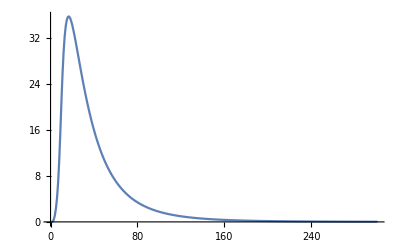

```mathematica
pts= Table[sigmapp[eCM,{p938,Δ1232}],{eCM,2.0,8.0,0.02}];
ListLinePlot[pts,PlotRange->All]
```

```mathematica
InGroupsOf[n_][table_]:=
Table[Table[table[[i]],{i,start,Min[start+n-1,Length[table]]}],{start,1,Length[table],n}];
```

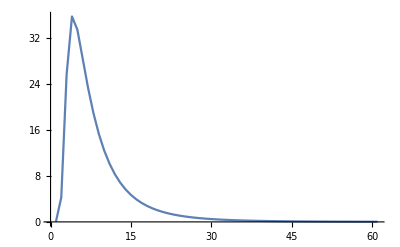

```mathematica
stream=OpenWrite[atNotebook["pts.txt"],FormatType->StandardForm];
Evaluate@Map[Apply[Write[stream,StringRiffle[ToString/@#]]]&,InGroupsOf[7]@(Second/@pts)];
Close[stream];
```

```mathematica
ps~Join~Δs
```

{p1535,p1650,p1520,p1700,p1675,p1440,p1710,p1720,p1680,Δ1620,Δ1700,Δ1910,Δ1600,Δ1920,Δ1905,Δ1950}

Calculating aN for p1535

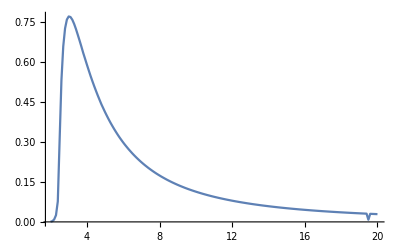

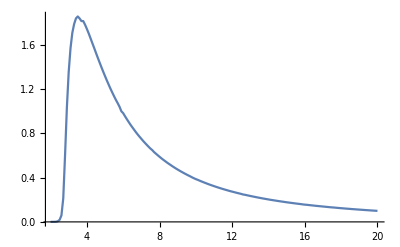

Calculating aN for p1650

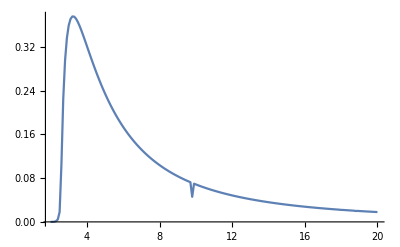

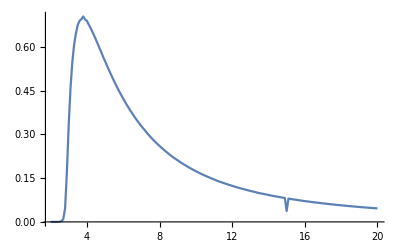

Calculating aN for p1520

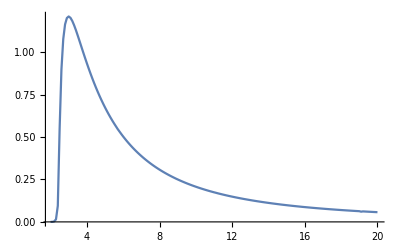

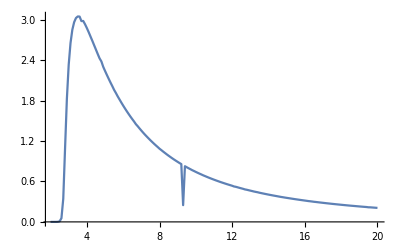

Calculating aN for p1700

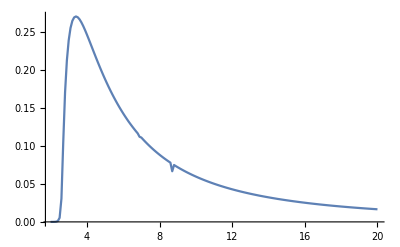

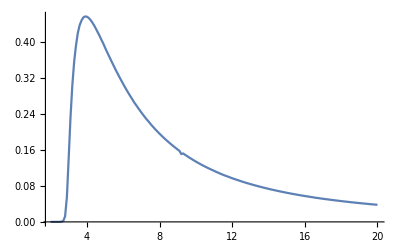

Calculating aN for p1675

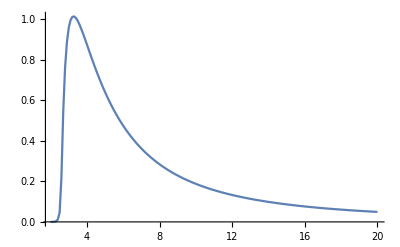

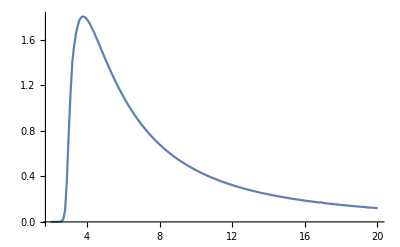

Calculating aN for p1440

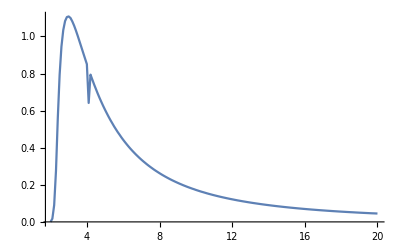

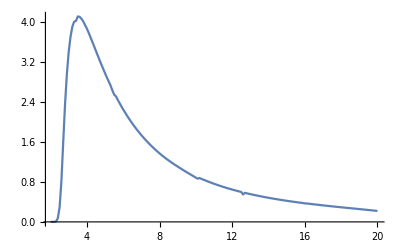

Calculating aN for p1710

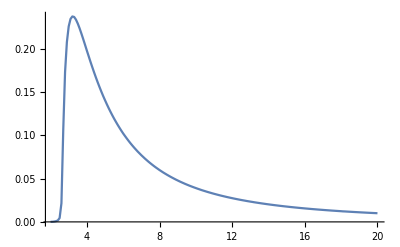

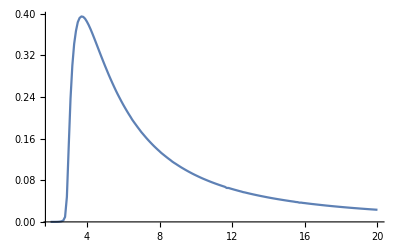

Calculating aN for p1720

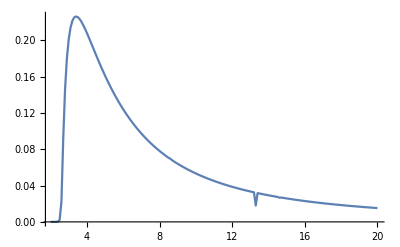

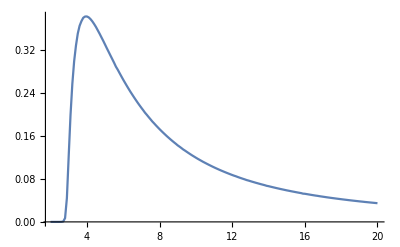

Calculating aN for p1680

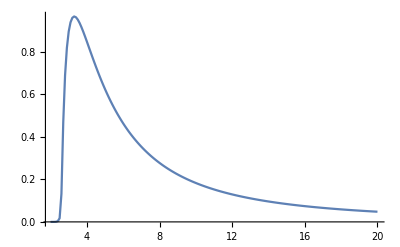

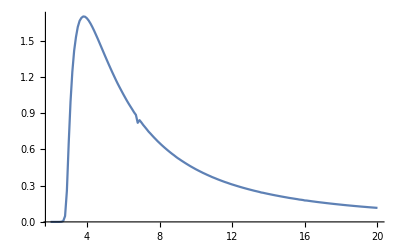

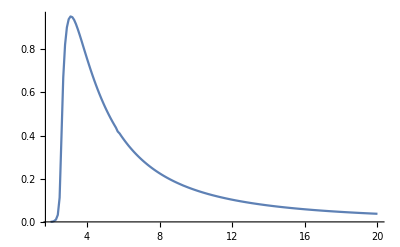

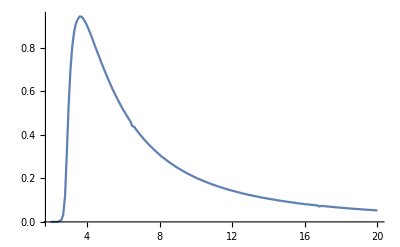

Calculating aN for Δ1700

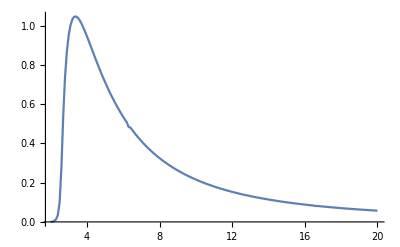

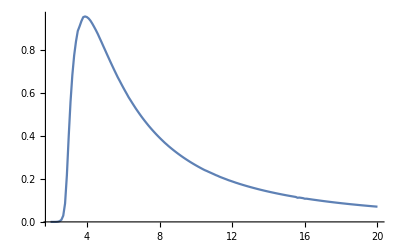

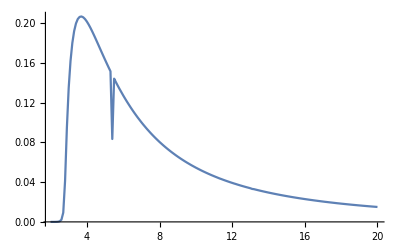

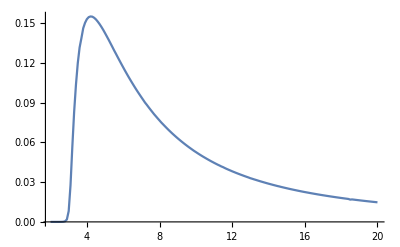

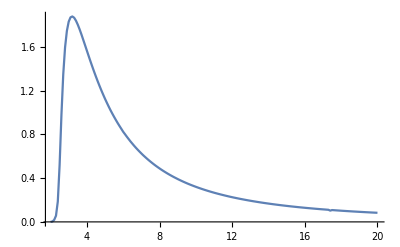

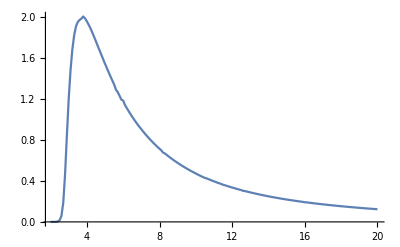

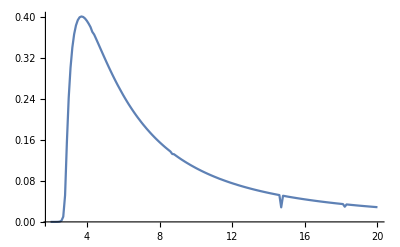

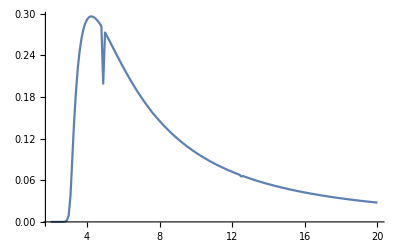

```mathematica
Table[
Block[{lBound=2.0,rBound=20.0},
Module[{pts},
pts=Quiet@Monitor[
Table[{eCM,sigmapp[eCM,{hA,hB}]},{eCM,lBound,rBound,.1}],
{{hA,hB},ProgressIndicator[eCM,{lBound,rBound}],eCM}
];
Block[{stream=OpenWrite[atNotebook["brFactor_"<>ToString[hA]<>ToString[hB]],FormatType->StandardForm]},
Evaluate@Map[Apply[Write[stream,StringRiffle[ToString/@#]]]&,InGroupsOf[7]@(If[#<10^-6,0.,#]&/@Second/@pts)];
Close[stream];
];
Print@ListLinePlot[pts,PlotRange->All];
];
]
,{hB,ps~Join~Δs},{hA,{p938,Δ1232}}
];
```

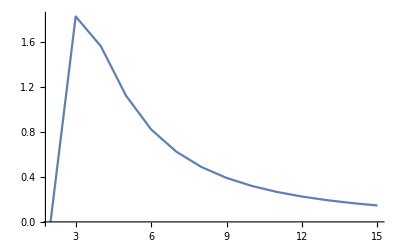

```mathematica
ptspΔ1600=Quiet@Monitor[
Table[{eCM,sigmapp[eCM,{p938,Δ1600}]},{eCM,2.0,15.0,1.}],
{ProgressIndicator[eCM,{2.0,8.0}],eCM}
];
Block[{stream=OpenWrite[atNotebook["brFactorND.txt"],FormatType->StandardForm]},
Evaluate@Map[Apply[Write[stream,StringRiffle[ToString/@#]]]&,InGroupsOf[7]@(Second/@ptspΔ1600)];
Close[stream];
];
ListLinePlot[ptspΔ1600,PlotRange->All]
```

```mathematica
First@AbsoluteTiming[
ptspΔ=Monitor[
Table[{eCM,sigmapp[eCM,{p938,Δ1232}]},{eCM,2.,8.,0.01}],
{ProgressIndicator[eCM,{2.,8.}],eCM}
]
]
```

14.765

```mathematica
First@AbsoluteTiming[
ptsΔΔ=Monitor[
Table[{eCM,sigmapp[eCM,{Δ1232,Δ1232}]},{eCM,2.,8.,0.1}],
{ProgressIndicator[eCM,{2.,8.}],eCM}
]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

52.9581

```mathematica
First@AbsoluteTiming[
ptspΔstar=Monitor[
Table[{eCM,Sum[sigmapp[eCM,{p938,Δ}],{Δ,Δs}]},{eCM,2.,8.,0.1}],
{Δ,ProgressIndicator[eCM,{2.,8.}],eCM}
]
]
```

Calculating aN for Δ1620

Calculating aN for Δ1700

Calculating aN for Δ1905

Calculating aN for Δ1910

Calculating aN for Δ1920

Calculating aN for Δ1950

632.341

```mathematica
manypMeanpΔstar=Monitor[
Table[{Δ,Table[{eCM,pMean[eCM,{p938,Δ}]},{eCM,2.,8.,0.1}]},{Δ,Δs}],
{Δ,ProgressIndicator[eCM,{2.,8.}],eCM}
];
```

```mathematica
Second[xs_]:=xs[[2]];
```

```mathematica
pMeanTot=Transpose[{Table[eCM,{eCM,2.,8.,0.1}],Total@Table[Second/@p,{p,manypMeanpΔstar}]}]
```

{{2.,0.00019007},{2.1,0.000516126},{2.2,0.00172033},{2.3,0.00513909},{2.4,0.0161327},{2.5,0.055237},{2.6,0.203737},{2.7,0.548249},{2.8,1.01481},{2.9,1.67155},{3.,2.32778},{3.1,2.93258},{3.2,3.49518},{3.3,4.0291},{3.4,4.54147},{3.5,5.03687},{3.6,5.52006},{3.7,5.99211},{3.8,6.45303},{3.9,6.90655},{4.,7.35479},{4.1,7.79664},{4.2,8.23214},{4.3,8.66371},{4.4,9.09235},{4.5,9.51468},{4.6,9.93445},{4.7,10.3522},{4.8,10.7651},{4.9,11.1758},{5.,11.5833},{5.1,11.9863},{5.2,12.3947},{5.3,12.7929},{5.4,13.1973},{5.5,13.5954},{5.6,13.9929},{5.7,14.3863},{5.8,14.7792},{5.9,15.1721},{6.,15.5623},{6.1,15.9528},{6.2,16.3409},{6.3,16.7253},{6.4,17.1134},{6.5,17.4911},{6.6,17.8812},{6.7,18.2636},{6.8,18.6474},{6.9,19.029},{7.,19.4085},{7.1,19.7889},{7.2,20.1662},{7.3,20.5429},{7.4,20.9227},{7.5,21.2981},{7.6,21.6773},{7.7,22.0528},{7.8,22.4245},{7.9,22.7836},{8.,23.1748}}

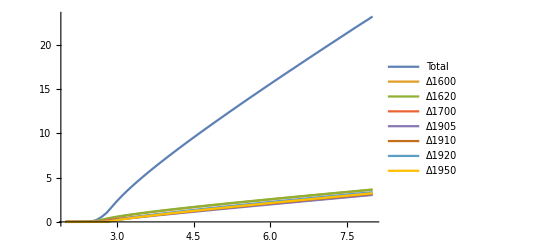

```mathematica
ListLinePlot[Prepend[pMeanTot]@manypMeanpΔstar,PlotLegends->Prepend["Total"]@(First/@manyptspΔstar),PlotRange->All]
```

```mathematica
First@AbsoluteTiming[
ptsppstar = Monitor[
Table[{eCM,Sum[sigmapp[eCM,{p938,p}],{p,ps}]},{eCM,2.,8.,0.1}],
{p,ProgressIndicator[eCM,{2.,8.}],eCM}
]
]
```

Calculating aN for p1440

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Calculating aN for p1520

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Calculating aN for p1535

Calculating aN for p1650

Calculating aN for p1675

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Calculating aN for p1680

Calculating aN for p1700

Calculating aN for p1710

Calculating aN for p1720

Calculating aN for p2190

Calculating aN for p2220

Calculating aN for p2250

788.602

```mathematica
First@AbsoluteTiming[
ptsΔpstar=Monitor[
Table[{eCM,Sum[sigmapp[eCM,{Δ1232,p}],{p,ps}]},{eCM,2.,8.,0.1}],
{p,ProgressIndicator[eCM,{2.,8.}],eCM}
]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

25999.3

```mathematica
First@AbsoluteTiming[
ptsΔΔstar=Monitor[
Table[{eCM,Sum[sigmapp[eCM,{Δ1232,Δ}],{Δ,Δs}]},{eCM,2.,8.,0.1}],
{Δ,ProgressIndicator[eCM,{2.,8.}],eCM}
]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

20684.2

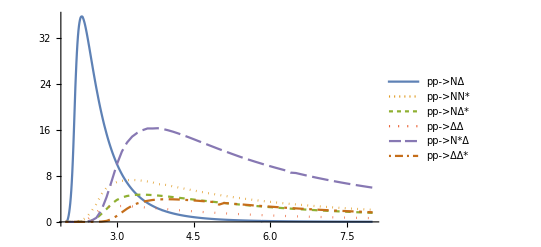

```mathematica
ListLinePlot[{ptspΔ,ptsppstar,ptspΔstar,ptsΔΔ, ptsΔpstar, ptsΔΔstar},
PlotStyle->{Automatic,Dashing[{0.001,0.01}],Dashing[{0.01,0.01}],Dashing[{0.001,0.02}],Dashing[{0.03,0.01}],Dashing[{0.005,0.01,0.02,0.01}]},
PlotRange->All,PlotLegends->{"pp->NΔ","pp->NN*","pp->NΔ*","pp->ΔΔ","pp->N*Δ","pp->ΔΔ*"} 
]
```

```mathematica
Export[atNotebook["sigmaNN2NDelta.dat"], ptspΔ];
Export[atNotebook["sigmaNN2NNstar.dat"], ptsppstar];
Export[atNotebook["sigmaNN2NDeltastar.dat"],ptspΔstar];
Export[atNotebook["sigmaNN2DeltaDelta.dat"],ptsΔΔ];
Export[atNotebook["sigmaNN2NstarDelta.dat"],ptsΔpstar];
Export[atNotebook["sigmaNN2DeltaDeltastar.dat"],ptsΔΔstar];
```

```mathematica
stream=OpenWrite[atNotebook["sigmaTotal.dat"],FormatType->StandardForm];
Evaluate@Map[Write[stream, #[[1]]," ", #[[2]]]&, ptsTotalf];
Close[stream];
```

```mathematica
{ptspΔf,ptsppstarf,ptspΔstarf,ptsΔΔf,ptsΔpstarf,ptsΔΔstarf}=Import[atNotebook["ppInelasticCrossSections.mx"]];
ptsTotalf=
Table[{ptspΔf[[i,1]], ptspΔf[[i,2]]+ptsppstarf[[i,2]]+ptspΔstarf[[i,2]]+ptsΔΔf[[i,2]]+ptsΔpstarf[[i,2]]+ptsΔΔstarf[[i,2]]}, {i,Length[ptspΔf]}];
```

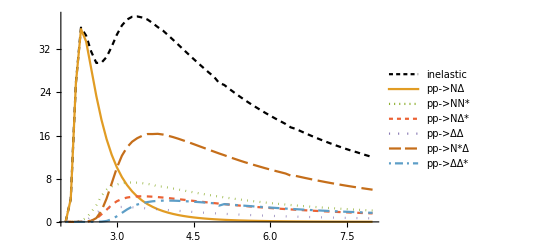

```mathematica
ListLinePlot[{ptsTotalf,ptspΔf,ptsppstarf,ptspΔstarf,ptsΔΔf,ptsΔpstarf,ptsΔΔstarf},
PlotStyle->{{Black,Dashing[{0.01,0.008}]},Automatic,Dashing[{0.001,0.01}],Dashing[{0.01,0.01}],Dashing[{0.001,0.02}],Dashing[{0.03,0.01}],Dashing[{0.005,0.01,0.02,0.01}]},
PlotRange->All,PlotLegends->{"inelastic","pp->NΔ","pp->NN*","pp->NΔ*","pp->ΔΔ","pp->N*Δ","pp->ΔΔ*"} 
]
```

```mathematica
ptsTotalf//MatrixForm
```

(2. | 0.0231985
2.1 | 4.25918
2.2 | 25.7155
2.3 | 35.9901
2.4 | 34.5053
2.5 | 31.5345
2.6 | 29.4478
2.7 | 29.4924
2.8 | 30.5397
2.9 | 32.4597
3. | 34.6596
3.1 | 36.3933
3.2 | 37.4837
3.3 | 37.9989
3.4 | 38.0549
3.5 | 37.8552
3.6 | 37.4859
3.7 | 36.8329
3.8 | 36.0895
3.9 | 35.4565
4. | 34.6049
4.1 | 33.7338
4.2 | 32.8414
4.3 | 31.9457
4.4 | 31.0646
4.5 | 30.1876
4.6 | 29.3271
4.7 | 28.4859
4.8 | 27.6627
4.9 | 26.882
5. | 25.7421
5.1 | 25.369
5.2 | 24.6329
5.3 | 23.9295
5.4 | 23.2455
5.5 | 22.5885
5.6 | 21.9606
5.7 | 21.3639
5.8 | 20.784
5.9 | 20.2123
6. | 19.6712
6.1 | 19.143
6.2 | 18.6391
6.3 | 18.1391
6.4 | 17.513
6.5 | 17.2201
6.6 | 16.7852
6.7 | 16.3622
6.8 | 15.9546
6.9 | 15.5585
7. | 15.1803
7.1 | 14.8108
7.2 | 14.4557
7.3 | 14.1126
7.4 | 13.7815
7.5 | 13.4593
7.6 | 13.1504
7.7 | 12.8775
7.8 | 12.5597
7.9 | 12.2777
8. | 12.)

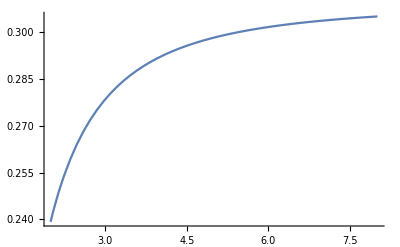

```mathematica
Plot[Γ[Δ1232,m],{m,2.,8.}]
```

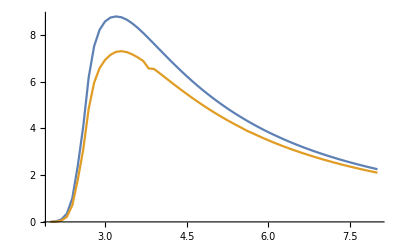

```mathematica
ListLinePlot[{ptsppstar,ptsppstarf}]
```

```mathematica
Γ[p1440,1.]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Total::normal: Nonatomic expression expected at position 1 in Total[pi].

First::normal: Nonatomic expression expected at position 1 in First[1.].

Throw::nocatch: Uncaught Throw[No nominal width found for 1.] returned to top level.

Hold[Throw[No nominal width found for 1.]]

```mathematica
decayProducts[p1440]
```

{{p938,pi},{Δ1232,pi},{p938,sigma}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

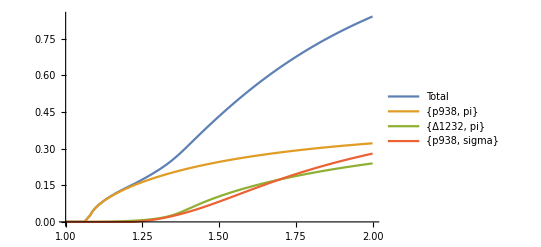

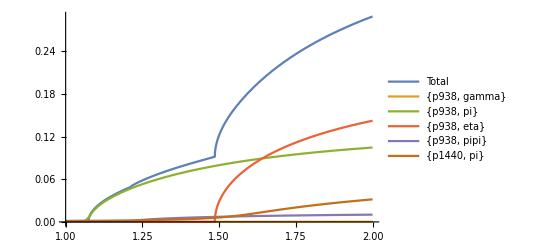

```mathematica
Block[{h=p1440},
Plot[Evaluate@Flatten@{Γ[h,m],Table[Γ[h,outs,m],{outs,decayProducts[h]}]},{m,1.,2.},PlotRange->{0,All},PlotLegends->Flatten@{"Total",ToString/@decayProducts[h]}]
]
```

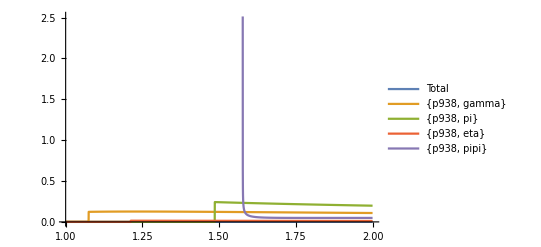

```mathematica
Block[{h=p1535},
Plot[Evaluate@{Table[Γ[h,outs,m]/Sqrt[m-Total[m0/@outs]],{outs,decayProducts[h]}]},{m,1.,2.},PlotRange->{0,All},PlotLegends->Flatten@{"Total",ToString/@decayProducts[h]}]
]
```